```mathematica
n=.
```

```mathematica
n[x_]:=CDF[NormalDistribution[0,1],x]
```

```mathematica
v[t_,x_,s_]:=Max[x,0]+n[d[t,x,s]]-(1+Abs[x])n[d[t,x,s]-s Sqrt[t]]+1/2(d[t,x,s]s Sqrt[t]-1)n[d[t,x,s]]+1/2(1+Abs[x])n[d[t,x,s]-s Sqrt[t]]+s/2 Sqrt[t]ns[d[t,x,s]];
```

```mathematica
Exit[]
```

```mathematica
ns[x_]:=CDF[NormalDistribution[0,1],x];
```

```mathematica
d[t_,x_,s_]:=(-Log[1+Abs[x]]+s^2/2 t)/s/Sqrt[t]
```

```mathematica
t=1;x=0;s=0.3;100*v[t,x,s]
```

15.6152

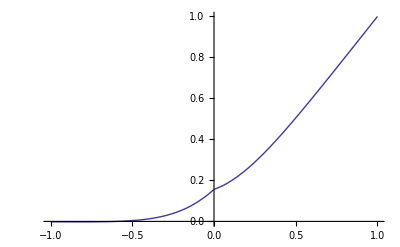

```mathematica
Plot[v[1,x1,s],{x1,-1,1}]
```

```mathematica
Log[E]
```

1